```mathematica
fD1 = Import["D:\\Kami\\git_folder\\notes_5sem\\rqc\\data_processing_1\\D1_v1.csv"];
fD2 = Import["D:\\Kami\\git_folder\\notes_5sem\\rqc\\data_processing_1\\D2_v1.csv"];
```

```mathematica
fD2 = Flatten@fD2;
fD1 = Flatten@fD1;
```

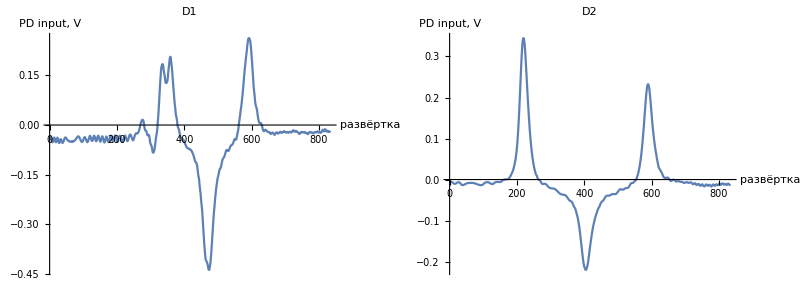

```mathematica
scale = 240;
image = Multicolumn[{
ListPlot[fD1, PlotRange->Full, Joined->True, ImageSize->{scale, scale}, AspectRatio->1,
PlotLabel->"D1", AxesLabel->{"развёртка", "PD input, V"}],
ListPlot[fD2, PlotRange->Full, Joined->True, ImageSize->{scale, scale}, AspectRatio->1,
PlotLabel->"D2", AxesLabel->{"развёртка", "PD input, V"}]
}]
(*Export[NotebookDirectory[]<>"D12.pdf", image]*)
```

## Фитирование гауссом

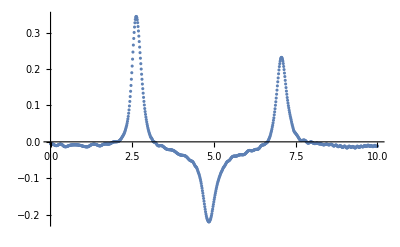

```mathematica
data = Transpose[{Range[0,10, 10./(Length@fD2-1)], Flatten@fD2}];
ListPlot[data, PlotRange->All]
```

{a→0.333467,x0→2.63396,σ→0.2127,c2→-0.00250756}

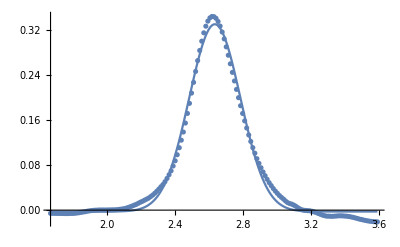

```mathematica
fit = FindFit[data⟦140;;300⟧, a Exp[-(x-x0)^2/σ^2]+ c2, {{a, 0.33}, {x0, 2.6}, {σ, 0.21}, c2}, x]
{aV1, x0V1, σV1, c2V1} = {a, x0, σ, c2}/.fit;
f1[x_] :=  aV1 Exp[-(x-x0V1)^2/σV1^2] + c2V1;
Show[{
Plot[f1[x], {x, data⟦140⟧⟦1⟧, data⟦300⟧⟦1⟧}, PlotRange->All],
ListPlot[data⟦140;;300⟧, PlotRange->All]
}]
```

## Фитирование лоренцем 1

```mathematica
xs = Range[0,10, 10./(Length@fD2-1)];
data = Transpose[{xs, Flatten@fD2}];
ListPlot[data, PlotRange->All]
```

-Graphics-

{a→0.3823,x0→2.6318,σ→0.163662,c2→-0.0283009}

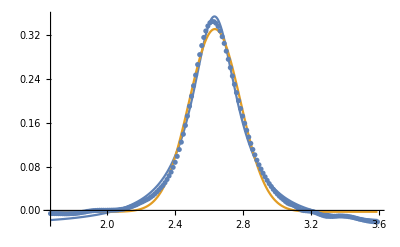

```mathematica
fit = FindFit[data⟦140;;300⟧, {a σ^2/((x-x0)^2+σ^2) + c2}, {{a, 0.37}, {x0, 2.63}, {σ, 0.135}, c2}, x]
{aV2, x0V2, σV2, c2V2} = {a, x0, σ, c2}/.fit;
f2[x_] := aV2 σV2^2/((x-x0V2)^2+σV2^2) + c2V2;
Show[{
Plot[{f2[x],f1[x]}, {x, data⟦140⟧⟦1⟧, data⟦300⟧⟦1⟧}, PlotRange->All],
ListPlot[data⟦140;;300⟧, PlotRange->All]
}]
```

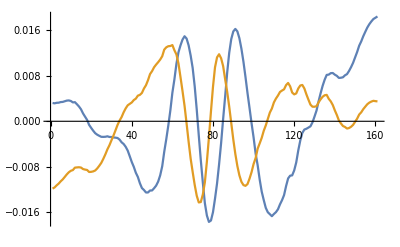

```mathematica
ListPlot[{
Map[f1, xs⟦140;;300⟧]-(Flatten@fD2)⟦140;;300⟧,
Map[f2, xs⟦140;;300⟧]-(Flatten@fD2)⟦140;;300⟧
}, Joined->True]
```

```mathematica
Min[Abs[tmpY-h/2]]
```

0.00023

```mathematica
tmpY = (Flatten@fD2)⟦140;;300⟧;
h = Max[tmpY];
i0 = Position[Abs[tmpY-h/2], Min[Abs[tmpY-h/2]]]⟦1⟧⟦1⟧;
2(x0V1-xs⟦140+i0⟧)
2 √Log[2] σV1
2(x0V2-xs⟦140+i0⟧)
2σV2
```

0.299767

0.354405

0.295677

0.327616

```mathematica
x0V2
```

2.63283

```mathematica
xs⟦i0⟧
```

1.92077

## Фитирование лоренцем 2

{a→0.3823,x0→2.6318,σ→0.163662,c2→-0.0283009}

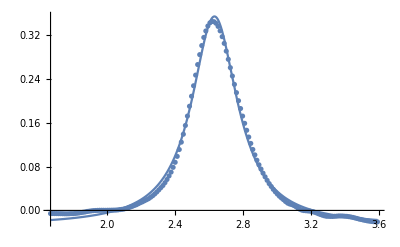

```mathematica
si = 140;
ei = 300;
fit = FindFit[data⟦si;;ei⟧, {a σ^2/((x-x0)^2+σ^2) + c2}, {{a, 0.37}, {x0, 2.6}, {σ, 0.135}, c2}, x]
{aV1, x0V1, σV1, c2V1} = {a, x0, σ, c2}/.fit;
f1[x_] := aV1 σV1^2/((x-x0V1)^2+σV1^2) + c2V1;
Show[{
Plot[f1[x], {x, data⟦si⟧⟦1⟧, data⟦ei⟧⟦1⟧}, PlotRange->All],
ListPlot[data⟦si;;ei⟧, PlotRange->All]
}]
```

{a→-0.200161,x0→4.85215,σ→0.237736,c2→-0.0209153}

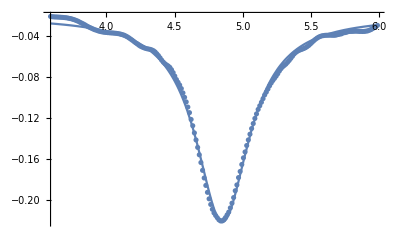

```mathematica
si = 300;
ei = 500;
fit = FindFit[data⟦si;;ei⟧, {a σ^2/((x-x0)^2+σ^2) + c2}, {{a, -0.37}, {x0, 4.8}, {σ, 0.135}, c2}, x]
{aV2, x0V2, σV2, c2V2} = {a, x0, σ, c2}/.fit;
f2[x_] := aV2 σV2^2/((x-x0V2)^2+σV2^2) + c2V2;
Show[{
Plot[f2[x], {x, data⟦si⟧⟦1⟧, data⟦ei⟧⟦1⟧}, PlotRange->All],
ListPlot[data⟦si;;ei⟧, PlotRange->All]
}]
```

{a→0.25956,x0→7.07568,σ→0.180932,c2→-0.0223874}

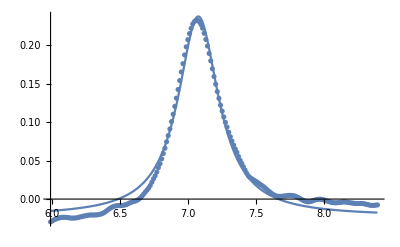

```mathematica
si = 500;
ei = 700;
fit = FindFit[data⟦si;;ei⟧, {a σ^2/((x-x0)^2+σ^2) + c2}, {{a, 0.37}, {x0, 7}, {σ, 0.135}, c2}, x]
{aV3, x0V3, σV3, c2V3} = {a, x0, σ, c2}/.fit;
f3[x_] := aV3 σV3^2/((x-x0V3)^2+σV3^2) + c2V3;
Show[{
Plot[f3[x], {x, data⟦si⟧⟦1⟧, data⟦ei⟧⟦1⟧}, PlotRange->All],
ListPlot[data⟦si;;ei⟧, PlotRange->All]
}]
```

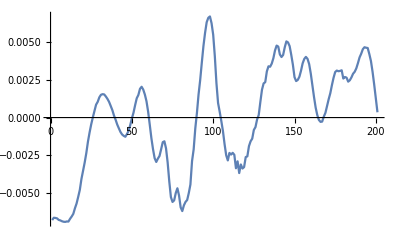

```mathematica
ListPlot[
Map[f2, xs⟦300;;500⟧]-(Flatten@fD2)⟦300;;500⟧
, Joined->True]
```

{a1→0.379467,x01→2.6321,σ1→0.159228,a2→-0.199551,x02→4.8527,σ2→0.255922,a3→0.260075,x03→7.07497,σ3→0.183302,c→-0.0214244}

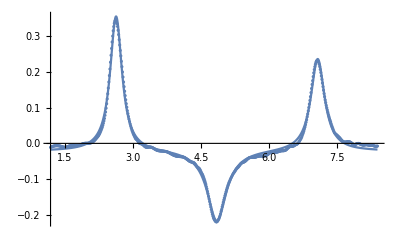

```mathematica
si = 100;
ei = 700;
fit = FindFit[data⟦si;;ei⟧, 
a1 σ1^2/((x-x01)^2+σ1^2)+a2 σ2^2/((x-x02)^2+σ2^2)+a3 σ3^2/((x-x03)^2+σ3^2)+ c, 
{{a1, aV1}, {x01, x0V1}, {σ1, σV1},
{a2, aV2}, {x02, x0V2}, {σ2,σV2},
{a3, aV3}, {x03, x0V3}, {σ3, σV3}, c},x]
f0[x_] :=a1 σ1^2/((x-x01)^2+σ1^2)+a2 σ2^2/((x-x02)^2+σ2^2)+a3 σ3^2/((x-x03)^2+σ3^2)+ c /. fit;
Show[{
Plot[f0[x], {x, data⟦si⟧⟦1⟧, data⟦ei⟧⟦1⟧}, PlotRange->All],
ListPlot[data⟦si;;ei⟧, PlotRange->All]
}]
```